```mathematica
ClearAll["Global`*"]
```

## Calculating the elliptic potential V(q) using the Jacobi Amplitude of module m

## The module in amu(q,k) is taken as k^2=m (as per the default behavior of the Wolfram implementation) -Graphics-

```mathematica
prepath="/Users/basavyr/Documents/Work/Repos/mathematica-useful-algorithms/Physics/Elliptic-Functions-New-Boson/Figures";
export[object_, name_, format_]:=Export[StringTemplate["``/``.``"][prepath,name, format],object, ImageResolution->1200];
```

```mathematica
mois={91,9,51};
oddspin=5.5;
A=N[1/(2*#)]&/@mois;
rad[theta_]:=N[theta*π/180];
```

Angular momentum vector j

```mathematica
j1[thetadeg_]:=oddspin*Cos[rad[thetadeg]];
j2[thetadeg_]:=oddspin*Sin[rad[thetadeg]];
```

Pre-Elliptic factors

```mathematica
Aterm[I_,thetadeg_]:=A[[2]](1-j2[thetadeg]/I)-A[[1]];
uterm[I_,thetadeg_]:=(A[[3]]-A[[1]])/Aterm[I,thetadeg];
v0term[I_,thetadeg_]:=-(A[[1]]*j1[thetadeg])/Aterm[I,thetadeg];
kterm[I_,thetadeg_]:=Sqrt[Abs[uterm[I,thetadeg]]];
```

Elliptic functions

```mathematica
phi[q_,k_]:=JacobiAmplitude[q,k^2];
sn[q_,k_]:=Sin[phi[q,k]];
cn[q_,k_]:=Cos[phi[q,k]];
dn[q_,k_]:=√(1-k^2 sn[q,k]^2);
```

Period for the elliptic functions-Graphics-

```mathematica
period[k_]:=Integrate[1/(√(1-k^2 Sin[t]^2)),{t,0,π/2}];
```

Elliptic Potential V_I(q)

```mathematica
Vq[q_,I_,thetadeg_]:=(I*(I+1)*kterm[I,thetadeg]^2+v0term[I,thetadeg]^2)*sn[q,kterm[I,thetadeg]]^2+(2I+1)*v0term[I,thetadeg]*cn[q,kterm[I,thetadeg]]*dn[q,kterm[I,thetadeg]];
```

Helper tools

```mathematica
linspace[a_,b_,n_]:=Table[N[i],{i,a,b,(b-a)/(n-1)}];
```

Tabulated values (tests)

```mathematica
(* Test values for the total angular momentum and the modulus k *)
spinvalues={22.5,18.5,14.5};
Ifit=spinvalues[[1]];
thetadegfit=-119;
kfit=kterm[Ifit,thetadegfit];
qrange[thetadeg_]:=Max[Table[4*period[kterm[spin,thetadeg]],{spin,spinvalues}]];
(* Tabulated values with the Elliptic values*)
qvalues[thetadeg_]:=linspace[-qrange[thetadeg],qrange[thetadeg],15];
(*phivalues=Table[SetPrecision[phi[qvalues[[i]],ktest],4],{i, 1, Length[qvalues]}];*)
(*snvalues=Table[SetPrecision[sn[qvalues[[i]],ktest],4],{i, 1, Length[qvalues]}];*)
(*cnvalues=Table[SetPrecision[cn[qvalues[[i]],ktest],4],{i, 1, Length[qvalues]}];*)
(*dnvalues=Table[SetPrecision[dn[qvalues[[i]],ktest],4],{i, 1, Length[qvalues]}];*)
(*vqvalues=Table[Vq[qvalues[[i]],Itest],{i, 1, Length[qvalues]}];*)
(*export[TableView[Table[{qvalues[[i]],ktest,phivalues[[i]],snvalues[[i]],cnvalues[[i]],dnvalues[[i]],vqvalues[[i]]},{i,1,Length[qvalues]}],Headers->{{"q","k","φ(q,k)","sn(q,k)", "cn(q,k)", "dn(q,k)","V_I(q)"},Automatic}],"elliptic-data","csv"];*)
```

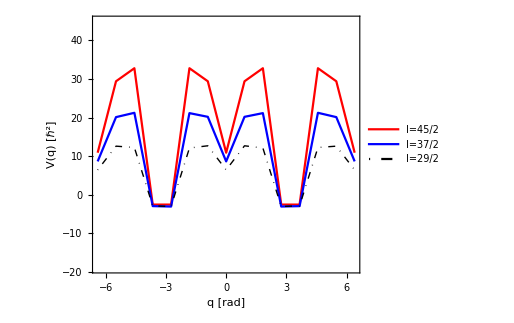

```mathematica
p1Fit[spinvalues_,thetadeg_]:=ListLinePlot[Table[Table[{q,Vq[q,spin,thetadeg]},{q,qvalues[thetadeg]}],{spin,spinvalues}],
Frame->True,
Axes->False,
FrameLabel->{"q [rad]","V(q) [ℏ^2]"},
AspectRatio->0.85,
FrameStyle->Directive[Black,Thick],
PlotStyle->{{Red},{Blue},{Black,Thick,DotDashed}},
LabelStyle->{19,Black,FontFamily->"Latin Modern Roman"},
ImageSize->380,
PlotLegends->Placed[Table[Style[StringTemplate["I=``/2"][Round[2*spin]],16],{spin,spinvalues}],{0.5,0.2}],
PlotRange->{-19,45}
];
(*p2FitThetaPi=Plot[{Vq[q,Itest],Vq[q,37/2],Vq[q,29/2]},{q,-qrange[Itest],qrange[Itest]}];*)
Show[p1Fit[spinvalues,thetadegfit]]
export[Show[p1Fit[spinvalues,thetadegfit]],"potential-fit-theta","pdf"];
```